x0:1.5 y0:2

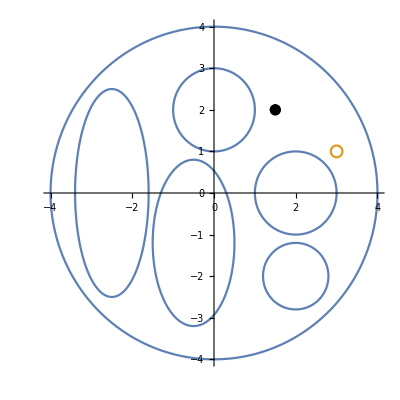

```mathematica
(*-----PROVA 1-----------------------------*)
(*dim=4;
b0[x_,y_]:=-((x)^2+(y)^2-dim^2);
b1[x_,y_]:=(x-1)^2+(y-1)^2-(3/4)^2;
b2[x_,y_]:=(x-1)^2+(y+1)^2-(2/4)^2;
b3[x_,y_]:=(x+1)^2+(y-1)^2-(4/4)^2;
obstacles[x_,y_]:=b0[x,y]*b1[x,y]*b2[x,y]*b3[x,y];
(*Target*)
xf = -1;
yf=-1;
f[x_,y_]:=((x-xf)^2+(y-yf)^2-(1/10)^2);*)
(*----------------------------------*)

(*-----PROVA 2-----------------------------*)
(*dim=10;
b0[x_,y_]:=-((x)^2+(y)^2-dim^2);
b1[x_,y_]:=(x-1)^2+(y-1)^2-(3/4)^2;
b2[x_,y_]:=(x-1)^2+(y+1)^2-(2/4)^2;
b3[x_,y_]:=(x+1)^2+(y-1)^2-(4/4)^2;
b4[x_,y_]:=(x+3)^2+(y-5)^2-(4/4)^2;
b5[x_,y_]:=(x-7)^2+(y)^2-(2)^2;
b6[x_,y_]:=(x-5)^2+(y-7)^2-(4/4)^2;
obstacles[x_,y_]:=b0[x,y]*b1[x,y]*b2[x,y]*b3[x,y]*b4[x,y]*b5[x,y]*b6[x,y];
(*Punto partenza*)
xxf = 6.5;
yyf= 7;
(*Punto di arrivo*)
f[x_,y_]:=((x-xxf)^2+(y-yyf)^2-(1/10)^2);*)
(*-----------------------------------------*)

(*-----PROVA 3-----------------------------*)
dim = 4;
b0[x_,y_]=((x)^2+(y)^2-dim^2);
b1[x_,y_]=(x-2)^2+(y)^2-(1)^2;
b2[x_,y_]=(x)^2+(y-2)^2-(1)^2;
b3[x_,y_,a_,b_]=((x+0.5)^2/a^2)+((y+1.2)^2/b^2)-1;
b4[x_,y_,a_,b_]=((x+2.5)^2/a^2)+((y)^2/b^2)-1;
b5[x_,y_]=(x-2)^2+(y+2)^2-(0.8)^2;
obstacles[x_,y_]=-b0[x,y]*b1[x,y]*b2[x,y]*b3[x,y,1,2]*b4[x,y,0.9,2.5]*b5[x,y];
xxf=3;
yyf=1;
(*Punto di arrivo*)
f[x_,y_]=((x- xxf)^2+(y-yyf)^2-(1/7)^2);
(*----------------------------------------------*)

(*-----PROVA 4-----------------------------*)
(*dim=10;
b0[x_,y_]:=-((x)^2+(y)^2-dim^2);
b1[x_,y_]:=(x-1)^2+(y-1)^2-(3/4)^2;
b2[x_,y_]:=(x-1)^2+(y+1)^2-(2/4)^2;
b3[x_,y_]:=(x+1)^2+(y-1)^2-(4/4)^2;
b4[x_,y_]:=(x+3)^2+(y-5)^2-(4/4)^2;
b5[x_,y_]:=(x-7.5)^2+(y)^2-(2)^2;
b6[x_,y_]:=(x-5)^2+(y-7)^2-(4/4)^2;
b7[x_,y_]:=(x)^2+(y+5)^2-(1.5)^2;
b8[x_,y_]:=(x+7)^2+(y)^2-(1.5)^2;
obstacles[x_,y_]:=b0[x,y]*b1[x,y]*b2[x,y]*b3[x,y]*b4[x,y]*b5[x,y]*b6[x,y]*b7[x,y]*b8[x,y];
xxf=5;
yyf=5;
(*Punto di arrivo*)
f[x_,y_]:=((x- xxf)^2+(y-yyf)^2-(1/10)^2);*)
(*----------------------------------------------*)

(*Punto iniziale e verifica validità*)
(*Thread: Convert equations for lists to lists of equations*)
validPointQ[x_,y_]:=(b0[x,y]<=0.01)&&And@@Thread[{b1[x,y],b2[x,y],b3[x,y,1,2],b4[x,y,0.9,2.5],b5[x,y]}>=0]&&(f[x,y]>=0);

findInitCond[]:=Module[{x,y,i=0,max=1000},
While[i<max,
	{x,y}=RandomReal[{-dim,dim},2];
	If[validPointQ[x,y],Return[{x,y}]];
	Print["Tentativo:",i];
	i++
];
Print["Errore: Nessun punto valido trovato"];
Abort[];
];

(*Calcolo traiettoria*)
{xx0,yy0}=findInitCond[];
x0=1.5;y0=2;
Print["x0:",x0," y0:",y0];

(*Grafico punto di partenza*)
start=ListPlot[{{x0,y0}},PlotStyle->Directive[Black,PointSize[0.02]]];

(*Grafico ostacoli*)
OB=ContourPlot[{obstacles[x,y]==0,f[x,y]==0},{x,-dim,dim},{y,-dim,dim},PlotPoints->100,PlotRange->{{-dim,dim},{-dim,dim}},AspectRatio->1];


Show[start,OB,PlotRange->{{-dim,dim},{-dim,dim}},AspectRatio->1,ImageSize->400]
```

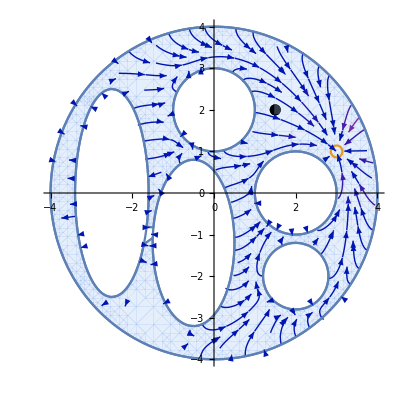

Gradiente iniziale: {0.0575864,-0.0236025}, modulo: 0.0622356 , modulo normalizzato: (ovviamente sarà 1)1.

```mathematica
(*Definizione del campo vettoriale*)
K=12;
ff = f[x,y];
oo = obstacles[x,y];
phi[x_,y_,k_]:=ff/Surd[ff^k+oo,k];

(*Calcolo gradiente*)
phiExpr=phi[x,y,K];

phix = D[phiExpr,x];
phiy = D[phiExpr,y];


allstreamVett = StreamPlot[{-phix,-phiy},
{x,-dim,dim},{y,-dim,dim},RegionFunction->Function[{x,y},obstacles[x,y]>=0],StreamPoints->1000,WorkingPrecision->100,PerformanceGoal->"Quality"
];



Show[start,allstreamVett,OB,PlotRange->{{-dim,dim},{-dim,dim}},AspectRatio->1,ImageSize->400]

(*Per vedere quanta spinta iniziale avrò*)
grad0={-phix/.{x->x0,y->y0},-phiy/.{x->x0,y->y0}};
Print["Gradiente iniziale: ",grad0,", modulo: ",Norm[grad0]", modulo normalizzato: (ovviamente sarà 1)",Normalize[Norm[grad0]]];
```

```mathematica
(*Risolvo l'equazione diff che genera la traiettoria*)
tf = 100;
l=0.1;
passi=Floor[tf/l];

(*Devo poter usarle nel dominio nel tempo*)
phixT = phix/.{x->x[t],y->y[t]};
phiyT = phiy/.{x->x[t],y->y[t]};

(*In linea teorica dovrei imporre questo sistema facendo una normale discesa del gradiente. Ma siccome può capitare di trovarsi in punti dove
{-phixT,-phiyT}[[1]] e {-phixT,-phiyT}[[2]] sono tendenti a zero, allora è come trovarsi in un punto di lavoro e quindi rimango lì. La cosa migliore è quella di normalizzare ciascuna componente del campo vettoriale phi cosicché riesco a muovermi anche in situazioni patologiche*)
(*eqs={
x'[t]=={-phixT,-phiyT}[[1]],
y'[t]=={-phixT,-phiyT}[[2]],
x[0]==x0,
y[0]==y0
};*)

(*Scelto di eseguire quello normalizzato per mantenere la direzione corretta ma per non inchiodarmi in punti dove |grad|->0*)
eqs={
x'[t]==l*Normalize[{-phixT,-phiyT}][[1]],
y'[t]==l*Normalize[{-phixT,-phiyT}][[2]],
x[0]==x0,
y[0]==y0
};

sol=NDSolve[eqs,{x[t],y[t]},{t,0,tf},Method->{"FixedStep",Method->"ExplicitEuler","StepSize"->l}];

(*Prendo tutti i punti della soluzione con passo l*)
trajPoints=Table[Evaluate[{x[t],y[t]}/. sol],{t,0,tf,l}];
(*Genero una traiettoria visiva come lista di punti*)
PP=ListLinePlot[trajPoints,AspectRatio->1,PlotStyle->Red,InterpolationOrder->1,PlotRange->{{-dim,dim},{-dim,dim}}];

Show[PP,start,OB,PlotRange->{{-dim,dim},{-dim,dim}},AspectRatio->1,ImageSize->400]
```

-Graphics-

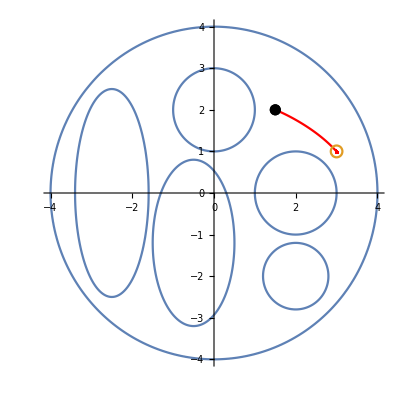

```mathematica
tf=100;
(*Definisco la lunghezza del passo (costante)*)
l=0.05;
(*Voglio intervalli di integrali tutti uguali e interi*)
passi=Floor[tf/l];

MetodoEulero[{gradX_,gradY_},{x0_,y0_},passi_,l_]:=Module[{punto={x0,y0},i,dx,dy,fx,fy,nuovoPunto,traj},
	traj=Reap[
        For[i=1,i<=passi,i++,
	 fx=gradX@@punto;
          fy=gradY@@punto;
	 (*Print["Passo ",i,": punto=",punto,", grad= ",{fx,fy}];*)
	(*Direzione nuovo punto normalizzato (così rispetto il numero dei passi)*)
	{dx,dy}=l*Normalize[{fx,fy}];
	nuovoPunto=punto+{dx,dy}; (*Passo al punto successivo*)
	punto=nuovoPunto;

	Sow[nuovoPunto];
	]
 ][[2,1]];
	Return[traj];
];


(*Siccome phix è una funzione del tipo phix del tipo f(x,y) ma non posso valutarla la phix in un punto, allora 
mi serve trovare un modo per tramutare una phix=f(x,y) in una phix[x,y]=f(x,y).Un modo per farlo è usare la Function[]*)

PHIX = Function[{x,y},Evaluate[phix]];
PHIY = Function[{x,y},Evaluate[phiy]];

gradNeg={Function[{x,y},-PHIX[x,y]],Function[{x,y},-PHIY[x,y]]};




traj=MetodoEulero[gradNeg,{x0,y0},passi,l];

(*Metto le condizioni iniziali all'inizio della traiettoria*)
traj=Prepend[traj,{x0,y0}];

PP=ListLinePlot[traj,AspectRatio->1,PlotStyle->Red,InterpolationOrder->1,PlotRange->{{-dim,dim},{-dim,dim}}];


Show[PP,start,OB,PlotRange->{{-dim,dim},{-dim,dim}},AspectRatio->1,ImageSize->400]
```